```mathematica
data=Import["C:\\Users\\pcarz\\AppData\\Local\\Packages\\CanonicalGroupLimited.UbuntuonWindows_79rhkp1fndgsc\\LocalState\\rootfs\\home\\pcarzon\\Intro_to_Cpp\\gluon_energy_dist_test.dat"];
```

```mathematica
data[[All,1]]
```

```mathematica
ClearAll[CreateHist]
CreateHist[x_, y_]:=Module[{Hist},Hist =Transpose[{x,y}]]
```

```mathematica
data1=CreateHist[data[[All,1]],data[[All,2]]];
data2=CreateHist[data[[All,1]],data[[All,3]]];
```

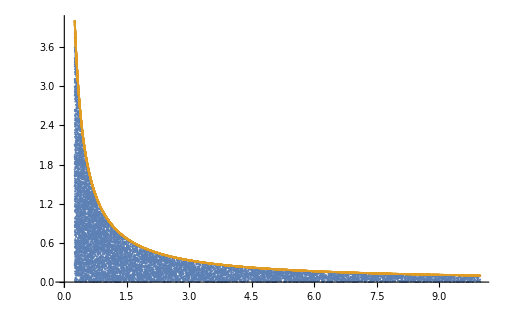

```mathematica
ListPlot[{data1,data2}]
```